## Лабораторная работа №4 6 семестр Карлович Алексей, Кирилло Дмитрий, Логвиненко Арина 3 курс, 5а группа ММФ БГУ Вариант 2

```mathematica
α= 0.1*k;
k=4;
```

```mathematica
A={{2,1,α},
{α,5,0.72},
{-1.2,3,1.7}};
```

```mathematica
f={-2.9,-0.7, -9.86};
```

```mathematica
A//MatrixForm
```

(2 | 1 | 0.4
0.4 | 5 | 0.72
-1.2 | 3 | 1.7)

```mathematica
ϵ=1/2 10^-4;
```

### 1.

```mathematica
A⟦3⟧=2Last@A + A⟦1⟧-A⟦2⟧
```

{-0.8,2,3.08}

```mathematica
A//MatrixForm
```

(2 | 1 | 0.4
0.4 | 5 | 0.72
-0.8 | 2 | 3.08)

```mathematica
f⟦3⟧=2f⟦3⟧+f⟦1⟧-f⟦2⟧;
```

```mathematica
f
```

{-2.9,-0.7,-21.92}

### 2.

```mathematica
(DD=DiagonalMatrix[Diagonal[A]])//MatrixForm
```

(2. | 0. | 0.
0. | 5. | 0.
0. | 0. | 3.08)

```mathematica
(CC=Inverse[DD])//MatrixForm
```

(0.5 | 0. | 0.
0. | 0.2 | 0.
0. | 0. | 0.324675)

```mathematica
(BB=IdentityMatrix[3]-CC.A)//MatrixForm
```

(0. | -0.5 | -0.2
-0.08 | 0. | -0.144
0.25974 | -0.649351 | 0.)

```mathematica
g=CC.f
```

{-1.45,-0.14,-7.11688}

```mathematica
(*норма ∞*)
```

```mathematica
NormInf[B_]:=Max[Total[Abs[B],{2}]]
```

```mathematica
NormInf[BB]
```

0.909091

```mathematica
(1-NormInf[BB])/NormInf[BB] ϵ
```

5.×10^-6

```mathematica
(*Jacobi*)
```

```mathematica
res=Block[
{x0=g,x1,step=0,hist={g}},
While[
True,
step++;
x1 = BB.x0+g;
If[NormInf[x1-x0]<(1-NormInf[BB])/NormInf[BB] ϵ,Break[]];
x0=x1;
AppendTo[hist,x1];
];
{hist,x1}
]
```

{{{-1.45,-0.14,-7.11688},{0.0433766,1.00083,-7.4026},{-0.469896,0.922504,-7.75551},{-0.360151,1.01438,-7.83796},{-0.3896,1.01748,-7.86912},{-0.384915,1.02432,-7.87878},{-0.386405,1.02534,-7.882},{-0.386268,1.02592,-7.88305},{-0.38635,1.02606,-7.88339},{-0.386351,1.02612,-7.88351},{-0.386357,1.02613,-7.88354},{-0.386358,1.02614,-7.88356}},{-0.386358,1.02614,-7.88356}}

```mathematica
First@res//Length
```

12

```mathematica
SuperStar[x]=Last@res
```

{-0.386358,1.02614,-7.88356}

### 3.

```mathematica
A={{2,1,α},
{α,5,0.72},
{-1.2,3,1.7}};
```

```mathematica
f={-2.9,-0.7, -9.86};
```

```mathematica
A.SuperStar[x]-f
```

{2.20652×10^-7,-3.01335×10^-6,3.60568×10^-7}

```mathematica
NormInf[A.SuperStar[x]-f]
```

3.01335×10^-6

### *

```mathematica
Norm1[A_]:=Max[Total[Abs[A],{1}]];
Norm2[A_]:=√Max[Eigenvalues[Transpose[A].A]];(*возможно надо поменять*)
```

```mathematica
NormInf[{{p,q},{q,p}}]
```

Abs[p]+Abs[q]

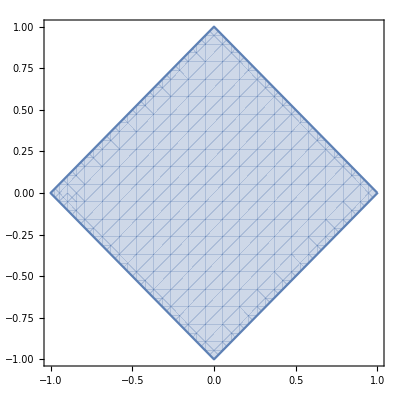

```mathematica
RegionPlot[NormInf[{{p,q},{q,p}}]<1,{p,-1,1},{q,-1,1}]
```

```mathematica
NormInf[{{p,q},{-q,p}}]
```

Abs[p]+Abs[q]

```mathematica
RegionPlot[NormInf[{{p,q},{-q,p}}]<1,{p,-1,1},{q,-1,1}]
```

-Graphics-

```mathematica
RegionPlot[Norm1[{{p,q},{q,p}}]<1,{p,-1,1},{q,-1,1}]
```

-Graphics-

```mathematica
RegionPlot[Norm1[{{p,q},{-q,p}}]<1,{p,-1,1},{q,-1,1}]
```

-Graphics-

```mathematica
RegionPlot[Norm2[{{p,q},{q,p}}]<1,{p,-1,1},{q,-1,1}]
```

-Graphics-

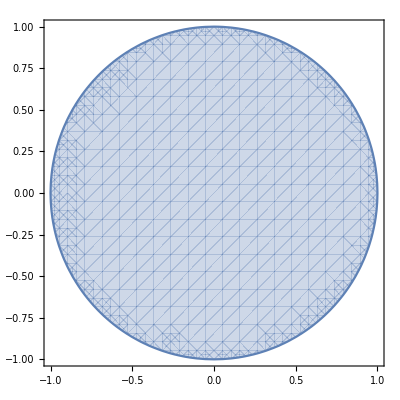

```mathematica
RegionPlot[Norm2[{{p,q},{-q,p}}]<1,{p,-1,1},{q,-1,1}]
```

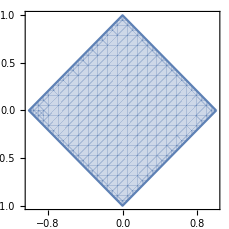

```mathematica
RegionPlot[And@@(#<1&/@Abs[Eigenvalues[{{p,q},{q,p}}]]),{p,-1,1},{q,-1,1}]
```

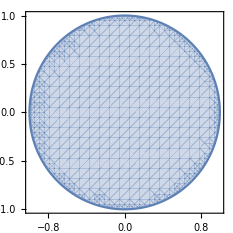

```mathematica
RegionPlot[And@@(#<1&/@Abs[Eigenvalues[{{p,q},{-q,p}}]]),{p,-1,1},{q,-1,1}]
```